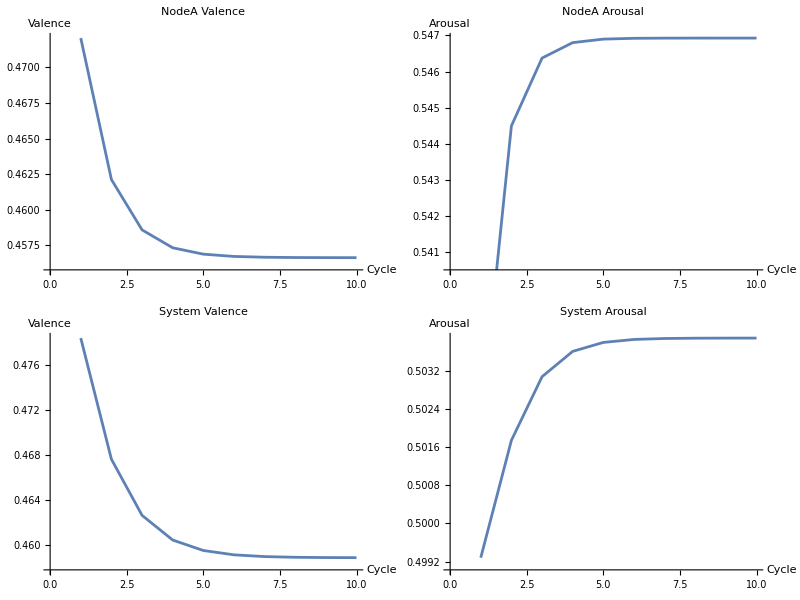

```mathematica
(* Define custom probabilistic OR function *)
customOr[x_,y_]:=1-(1-x)*(1-y)

(* Constants *)
λ=0.65; (* Modulation constant, less than 1 *)

(* Initial node affinities: valence and arousal *)
nodes=<|
   "NodeA"-><|"Valence"->0.5,"Arousal"->0.5|>,
   "NodeB"-><|"Valence"->0.5,"Arousal"->0.5|>
   (* Add more nodes as needed *)
   |>; 

(* Initial system-wide affinity values *)
systemAffinity=<|"Valence"->0.5,"Arousal"->0.5|>;

(* Function to update node affinity based on predictive link *)
updateNodeAffinity[node_,activation_,fRevised_,cRevised_]:=Module[
  {vInitial,aInitial,expectation,vNew,aNew},
  vInitial=nodes[node]["Valence"];
  aInitial=nodes[node]["Arousal"];
  expectation=cRevised *(fRevised - 0.5)+ 0.5; (* Simplified expectation calculation *)
  vNew=customOr[vInitial,expectation]*λ;
  aNew=customOr[aInitial,activation]*λ;
  nodes[node]=<|"Valence"->vNew,"Arousal"->aNew|>;
];

(* Function to update system-wide affinity based on active nodes *)
updateSystemAffinity[activeNodes_]:=Module[
  {vSystem,aSystem,vNode,aNode,factor},
  vSystem=systemAffinity["Valence"];
  aSystem=systemAffinity["Arousal"];
  factor=1/Length[activeNodes];
  
  Do[
   vNode=nodes[node]["Valence"];
   aNode=nodes[node]["Arousal"];
   vSystem=customOr[vSystem,vNode*factor]*λ;
   aSystem=customOr[aSystem,aNode*factor]*λ;
   ,{node,activeNodes}];
  
  systemAffinity=<|"Valence"->vSystem,"Arousal"->aSystem|>;
];

(* Simulate updates over several cycles and collect data *)
cycles=10;
nodeValenceData=Table[{},{Length[nodes]}];
nodeArousalData=Table[{},{Length[nodes]}];
systemValenceData={};
systemArousalData={};
nodeNames=Keys[nodes];

Do[
  updateNodeAffinity["NodeA",0.65,0.45,0.95];
  updateSystemAffinity[{"NodeA"}];
  
  AppendTo[nodeValenceData[[1]],nodes["NodeA"]["Valence"]];
  AppendTo[nodeArousalData[[1]],nodes["NodeA"]["Arousal"]];
  
  AppendTo[systemValenceData,systemAffinity["Valence"]];
  AppendTo[systemArousalData,systemAffinity["Arousal"]];
  
  ,{cycle,cycles}];

(* Plot valence and arousal changes over cycles for nodes *)
valencePlots=Table[
   ListLinePlot[nodeValenceData[[i]],
    PlotLabel->nodeNames[[i]] <> " Valence",
    AxesLabel->{"Cycle","Valence"}],{i,Length[nodeNames]}];

arousalPlots=Table[
   ListLinePlot[nodeArousalData[[i]],
    PlotLabel->nodeNames[[i]] <> " Arousal",
    AxesLabel->{"Cycle","Arousal"}],{i,Length[nodeNames]}];

(* Plot system-wide valence and arousal *)
systemValencePlot=ListLinePlot[systemValenceData,
   PlotLabel->"System Valence",AxesLabel->{"Cycle","Valence"}];

systemArousalPlot=ListLinePlot[systemArousalData,
   PlotLabel->"System Arousal",AxesLabel->{"Cycle","Arousal"}];

(* Display plots *)
Grid[{{valencePlots[[1]],arousalPlots[[1]]},
      {systemValencePlot,systemArousalPlot}}]
```